```mathematica
Ank = 2 / 7 * (x * y)*(7-x)*(2 - y)*Sin[Pi * n * x / 7] * Sin[Pi * k * y / 2]
```

2/7 (7-x) x (2-y) y Sin[(n π x)/7] Sin[(k π y)/2]

```mathematica
AnkX = Integrate[Ank, {y, 0, 2}]
```

(16 (-7+x) x (-2+2 Cos[k π]+k π Sin[k π]) Sin[(n π x)/7])/(7 k^3 π^3)

```mathematica
AnkXY = Integrate[AnkX, {x, 0, 7}]
```

(784 (-2+2 Cos[k π]+k π Sin[k π]) (-2+2 Cos[n π]+n π Sin[n π]))/(k^3 n^3 π^6)

```mathematica
FullSimplify[%]
```

(784 (-2+2 Cos[k π]+k π Sin[k π]) (-2+2 Cos[n π]+n π Sin[n π]))/(k^3 n^3 π^6)

```mathematica
ReplaceAll[AnkXY, {k->3 ,n->3}]
```

12544/(729 π^6)

-Graphics3D-

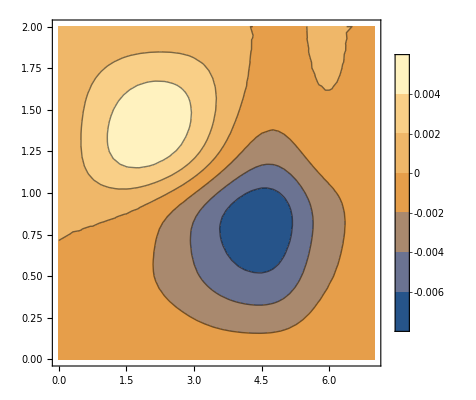

-Graphics3D-

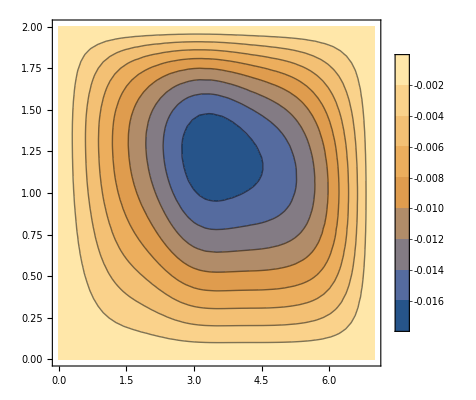

-Graphics3D-

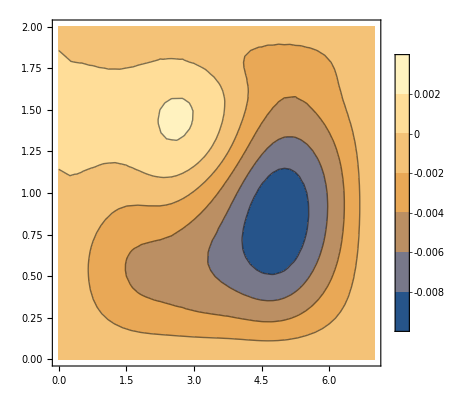

```mathematica
u[x_, y_, t_]:=Sum[Sum[12544/((2*n+1)^3 * (2*k+1)^3 * Pi^6) * Cos[7 * Sqrt[Pi^2 * (2*n+1)^2 / 49 + Pi^2 * (2*k + 1)^2 / 4] * t] * Sin[Pi * n * x / 7] * Sin[Pi * k * y / 2], {k, 0, 10}], {n, 0, 10}]
Plot3D[Evaluate[u[x, y, 0.5]], {x, 0, 7}, {y, 0, 2}, AxesLabel->{x, y, "u(x, y, 0.5)"}]
ContourPlot[Evaluate[u[x, y, 0.5]], {x, 0, 7}, {y, 0, 2}, PlotLegends->Automatic]
Plot3D[Evaluate[u[x, y, 1]], {x, 0, 7}, {y, 0, 2}, AxesLabel->{x, y, "u(x, y, 1)"}]
ContourPlot[Evaluate[u[x, y, 1]], {x, 0, 7}, {y, 0, 2}, PlotLegends->Automatic]
Plot3D[Evaluate[u[x, y, 5]], {x, 0, 7}, {y, 0, 2}, AxesLabel->{x, y, "u(x, y, 5)"}]
ContourPlot[Evaluate[u[x, y, 5]], {x, 0, 7}, {y, 0, 2}, PlotLegends->Automatic]
```